```mathematica
ClearAll["Global`*"]
```

### Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

#### Helper func

```mathematica
makeErrorData[x_,y_,yErr_]:=Module[{zeList,xy,errorB},
xy=Partition[Riffle[x,y],2];
errorB=Map[ErrorBar,yErr];
zeList=Partition[Riffle[xy,errorB],2]
];
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
orbit=1612;
```

## Initialize J-V, J_E-V data

### pot offset (in V)?

```mathematica
potTFactor=0;
```

### And the data ...

```mathematica
(*Attempt 2—corrected ion pots*)
```

```mathematica
time={"12:00:04.250","12:00:04.881","12:00:05.511","12:00:06.142","12:00:06.773","12:00:07.403","12:00:08.034","12:00:08.664","12:00:09.295","12:00:09.926","12:00:10.556","12:00:11.187","12:00:11.817","12:00:12.448","12:00:13.079","12:00:13.709","12:00:14.340","12:00:14.970","12:00:15.601","12:00:16.232","12:00:16.862","12:00:17.493","12:00:18.124","12:00:18.754","12:00:19.385","12:00:20.015","12:00:20.646","12:00:21.277","12:00:21.907","12:00:22.538","12:00:23.169","12:00:23.799","12:00:24.430","12:00:25.060","12:00:25.691","12:00:26.322","12:00:26.952","12:00:27.583","12:00:28.213","12:00:28.844","12:00:29.475","12:00:30.105","12:00:30.736","12:00:31.367","12:00:31.997","12:00:32.628","12:00:33.259","12:00:33.889","12:00:34.520","12:00:35.150","12:00:35.781","12:00:36.412","12:00:37.042","12:00:37.673","12:00:38.304","12:00:38.934","12:00:39.565","12:00:40.196","12:00:40.826","12:00:41.457","12:00:42.088","12:00:42.718","12:00:43.349","12:00:43.979","12:00:44.610","12:00:45.241","12:00:45.871","12:00:46.502","12:00:47.133","12:00:47.763","12:00:48.394","12:00:49.025","12:00:49.655","12:00:50.286","12:00:50.917","12:00:51.547","12:00:52.178","12:00:52.809","12:00:53.439","12:00:54.070","12:00:54.701","12:00:55.331","12:00:55.962","12:00:56.593","12:00:57.223","12:00:57.854","12:00:58.485","12:00:59.115","12:00:59.746","12:01:00.377","12:01:01.007","12:01:01.638","12:01:02.269","12:01:02.899","12:01:03.530","12:01:04.161","12:01:04.791","12:01:05.422","12:01:06.053","12:01:06.683","12:01:07.314","12:01:07.945","12:01:08.575","12:01:09.206","12:01:09.837","12:01:10.467","12:01:11.098","12:01:11.729","12:01:12.359","12:01:12.990","12:01:13.621","12:01:14.251","12:01:14.882","12:01:15.513","12:01:16.144","12:01:16.774","12:01:17.405","12:01:18.036","12:01:18.666","12:01:19.297","12:01:19.928","12:01:20.558","12:01:21.189","12:01:21.820","12:01:22.450","12:01:23.081","12:01:23.712","12:01:24.343","12:01:24.973","12:01:25.604","12:01:26.235","12:01:26.865","12:01:27.496","12:01:28.127","12:01:28.757","12:01:29.388","12:01:30.019","12:01:30.650","12:01:31.280","12:01:31.911","12:01:32.542","12:01:33.172","12:01:33.803","12:01:34.434","12:01:35.064","12:01:35.695","12:01:36.326","12:01:36.957","12:01:37.587","12:01:38.218","12:01:38.849","12:01:39.479","12:01:40.110","12:01:40.741","12:01:41.372","12:01:42.002","12:01:42.633","12:01:43.264","12:01:43.894","12:01:44.525","12:01:45.156","12:01:45.787","12:01:46.417","12:01:47.048","12:01:47.679","12:01:48.309","12:01:48.940","12:01:49.571","12:01:50.202","12:01:50.832","12:01:51.463","12:01:52.094","12:01:52.725","12:01:53.355","12:01:53.986","12:01:54.617","12:01:55.247","12:01:55.878","12:01:56.509","12:01:57.140","12:01:57.770","12:01:58.401","12:01:59.032","12:01:59.663","12:02:00.293","12:02:00.924","12:02:01.555","12:02:02.186","12:02:02.816","12:02:03.447","12:02:04.078","12:02:04.708","12:02:05.339","12:02:05.970","12:02:06.601"};
pots={689.92,86.24,86.24,86.24,407.68,344.96,344.96,344.96,689.92,564.48,689.92,815.36,815.36,815.36,940.80,940.80,815.36,815.36,1128.96,689.92,1128.96,815.36,940.80,940.80,689.92,689.92,689.92,689.92,689.92,689.92,689.92,815.36,940.80,1128.96,1379.84,1379.84,1379.84,1400.00,1357.44,1429.12,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,851.20,790.72,777.28,840.00,840.00,1554.56,1554.56,1106.56,940.80,940.80,940.80,689.92,1010.24,1059.52,1008.00,1008.00,1008.00,1133.44,1133.44,1008.00,1008.00,790.72,678.72,543.20,344.96,344.96,344.96,235.20,203.84,235.20,407.68,344.96,172.48,172.48,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,235.20,282.24,101.92,203.84,282.24,407.68,407.68,235.20,203.84,282.24,344.96,407.68,407.68,407.68,344.96,344.96,282.24,235.20,203.84,141.12,86.24,101.92,172.48,235.20,407.68,470.40,562.80,605.92,724.64,749.28,835.52,840.00,913.92,913.92,913.92,913.92,777.28,566.72,678.72,529.76,417.76,604.80,86.24,235.20,235.20,282.24,172.48,117.60,344.96,564.48,815.36,815.36,800.80,592.48,564.48,407.68,344.96,344.96,344.96,282.24,235.20,203.84,117.60,86.24,86.24,282.24,282.24,282.24,282.24,282.24,282.24,235.20,172.48,101.92,689.92,689.92,689.92,689.92,564.48,470.40,689.92,564.48,815.36,815.36,86.24,86.24,564.48,689.92,564.48,564.48,815.36,815.36,689.92,564.48,564.48,86.24,117.60,235.20,282.24,815.36,689.92};
curs={0.123,0.170,0.150,0.169,0.184,0.173,0.156,0.210,0.287,0.314,0.334,0.329,0.327,0.341,0.322,0.369,0.388,0.370,0.336,0.324,0.303,0.291,0.286,0.291,0.310,0.380,0.448,0.520,0.696,0.903,1.059,1.308,1.488,1.686,1.705,1.833,1.813,1.275,0.906,0.911,1.106,1.112,1.008,0.987,0.913,0.950,0.874,0.945,0.783,0.806,0.820,0.835,0.860,1.033,1.865,2.051,1.628,0.956,0.908,0.811,0.788,0.886,0.850,0.855,0.818,0.787,0.810,0.761,0.648,0.598,0.519,0.586,0.553,0.418,0.294,0.134,0.153,0.176,0.258,0.411,0.470,0.584,0.561,0.559,0.536,0.559,0.632,0.509,0.574,0.642,0.596,0.782,0.815,0.746,0.986,0.751,0.300,0.456,0.620,1.019,1.165,0.957,0.761,0.986,1.645,1.784,2.023,2.043,1.852,1.961,1.666,1.466,1.369,0.895,0.738,1.193,1.190,1.459,1.831,1.996,1.770,1.686,1.846,1.754,1.759,1.625,1.577,1.517,1.322,1.369,1.276,1.144,1.259,1.090,0.891,0.807,0.514,0.299,0.322,0.479,0.651,0.543,1.284,1.987,2.762,2.530,2.089,1.240,1.400,1.271,1.379,1.271,1.123,1.009,1.156,0.894,0.777,0.420,0.718,1.288,1.085,1.129,1.309,1.252,1.134,1.089,0.957,0.643,0.300,0.263,0.223,0.179,0.177,0.167,0.160,0.148,0.142,0.170,0.238,0.189,0.136,0.125,0.138,0.138,0.106,0.104,0.100,0.105,0.098,0.156,0.442,0.869,1.311,1.123,0.934};
curErrs={0.014,0.013,0.016,0.020,0.019,0.020,0.016,0.021,0.019,0.023,0.024,0.023,0.025,0.026,0.021,0.030,0.030,0.030,0.026,0.030,0.026,0.022,0.024,0.024,0.032,0.028,0.028,0.038,0.041,0.042,0.046,0.053,0.061,0.057,0.068,0.065,0.064,0.046,0.040,0.039,0.046,0.047,0.042,0.043,0.036,0.044,0.038,0.055,0.046,0.033,0.043,0.046,0.038,0.047,0.085,0.087,0.093,0.049,0.050,0.054,0.047,0.057,0.053,0.051,0.054,0.052,0.048,0.051,0.048,0.044,0.047,0.050,0.056,0.041,0.036,0.030,0.026,0.052,0.034,0.039,0.058,0.058,0.057,0.056,0.047,0.064,0.067,0.045,0.085,0.078,0.065,0.069,0.069,0.112,0.107,0.089,0.049,0.061,0.074,0.126,0.163,0.111,0.101,0.164,0.128,0.099,0.133,0.126,0.112,0.133,0.131,0.121,0.051,0.042,0.042,0.042,0.047,0.055,0.063,0.062,0.070,0.055,0.062,0.063,0.059,0.061,0.056,0.056,0.187,0.110,0.119,0.103,0.095,0.141,0.129,0.087,0.025,0.031,0.030,0.036,0.033,0.027,0.059,0.081,0.133,0.098,0.086,0.062,0.074,0.059,0.034,0.040,0.034,0.031,0.032,0.028,0.022,0.028,0.030,0.035,0.045,0.032,0.042,0.034,0.029,0.029,0.028,0.027,0.063,0.034,0.048,0.032,0.031,0.046,0.057,0.027,0.063,0.030,0.017,0.020,0.025,0.016,0.024,0.019,0.014,0.012,0.013,0.013,0.013,0.016,0.020,0.026,0.033,0.028,0.029};
jes={0.100,0.114,0.132,0.137,0.146,0.142,0.122,0.174,0.270,0.298,0.346,0.326,0.341,0.370,0.336,0.389,0.398,0.397,0.358,0.339,0.312,0.292,0.272,0.248,0.267,0.274,0.332,0.391,0.497,0.633,0.789,1.075,1.435,1.818,1.934,2.025,2.065,1.338,0.780,0.737,0.865,0.759,0.618,0.559,0.467,0.495,0.431,0.510,0.387,0.421,0.446,0.465,0.482,0.646,1.573,1.778,1.374,0.695,0.647,0.550,0.516,0.581,0.563,0.588,0.586,0.544,0.529,0.478,0.359,0.311,0.242,0.264,0.252,0.176,0.127,0.079,0.085,0.088,0.112,0.156,0.173,0.205,0.202,0.201,0.187,0.194,0.207,0.176,0.190,0.236,0.216,0.281,0.264,0.245,0.357,0.303,0.135,0.188,0.274,0.481,0.529,0.346,0.277,0.378,0.719,0.807,0.915,0.890,0.744,0.744,0.576,0.497,0.444,0.313,0.276,0.381,0.399,0.559,0.857,1.089,1.024,1.021,1.188,1.219,1.199,1.006,0.964,0.927,0.795,0.835,0.709,0.581,0.669,0.547,0.405,0.366,0.254,0.200,0.209,0.267,0.322,0.290,0.675,1.240,2.103,1.985,1.547,0.738,0.899,0.769,0.725,0.751,0.684,0.573,0.555,0.452,0.370,0.292,0.397,0.667,0.661,0.626,0.660,0.586,0.547,0.501,0.438,0.353,0.250,0.225,0.204,0.177,0.160,0.156,0.142,0.132,0.147,0.162,0.163,0.154,0.122,0.113,0.128,0.121,0.096,0.113,0.103,0.091,0.117,0.119,0.171,0.314,0.655,0.927,0.680};
jeErrs={0.057,0.050,0.999,0.051,0.114,0.096,0.037,0.080,0.055,0.060,0.090,0.062,0.075,0.096,0.058,0.085,0.057,0.067,0.058,0.057,0.061,0.046,0.051,0.046,0.050,0.038,0.050,0.059,0.068,0.059,0.071,0.082,0.095,0.110,0.131,0.135,0.137,0.120,0.110,0.152,0.136,0.120,0.107,0.094,0.067,0.083,0.096,0.127,0.104,0.062,0.081,0.087,0.075,0.091,0.130,0.127,0.127,0.102,0.107,0.107,0.099,0.133,0.137,0.105,0.122,0.116,0.096,0.093,0.081,0.075,0.056,0.057,0.062,0.044,0.050,0.034,0.029,0.130,0.105,0.063,0.061,0.077,0.318,0.070,0.107,0.423,0.067,0.095,0.064,0.074,0.140,0.152,0.142,0.111,0.115,0.091,0.076,1.074,0.095,0.143,0.205,0.126,0.138,0.172,0.144,0.141,0.186,0.171,0.134,0.151,0.135,0.112,0.060,0.055,0.058,0.052,0.061,0.079,0.102,0.119,0.145,0.121,0.134,0.146,0.152,0.144,0.125,0.123,5.248,0.261,0.238,0.487,0.214,0.196,0.145,0.081,0.054,0.050,0.073,0.061,0.060,0.098,0.112,0.124,0.240,0.184,0.163,0.124,0.144,0.124,0.098,0.121,0.094,0.077,0.092,0.087,0.092,0.074,0.080,0.094,0.110,0.092,0.212,0.086,0.095,0.075,0.080,0.075,0.082,0.066,0.114,0.065,0.085,0.074,0.107,0.458,0.086,0.080,0.044,0.060,0.039,0.041,0.054,0.034,0.028,0.041,0.030,0.023,0.053,0.028,0.081,0.080,0.480,0.082,0.067};
```

```mathematica
(*Attempt 1*)
```

```mathematica
(*time={"12:00:04.250","12:00:04.881","12:00:05.511","12:00:06.142","12:00:06.773","12:00:07.403","12:00:08.034","12:00:08.664","12:00:09.295","12:00:09.926","12:00:10.556","12:00:11.187","12:00:11.817","12:00:12.448","12:00:13.079","12:00:13.709","12:00:14.340","12:00:14.970","12:00:15.601","12:00:16.232","12:00:16.862","12:00:17.493","12:00:18.124","12:00:18.754","12:00:19.385","12:00:20.015","12:00:20.646","12:00:21.277","12:00:21.907","12:00:22.538","12:00:23.169","12:00:23.799","12:00:24.430","12:00:25.060","12:00:25.691","12:00:26.322","12:00:26.952","12:00:27.583","12:00:28.213","12:00:28.844","12:00:29.475","12:00:30.105","12:00:30.736","12:00:31.367","12:00:31.997","12:00:32.628","12:00:33.259","12:00:33.889","12:00:34.520","12:00:35.150","12:00:35.781","12:00:36.412","12:00:37.042","12:00:37.673","12:00:38.304","12:00:38.934","12:00:39.565","12:00:40.196","12:00:40.826","12:00:41.457","12:00:42.088","12:00:42.718","12:00:43.349","12:00:43.979","12:00:44.610","12:00:45.241","12:00:45.871","12:00:46.502","12:00:47.133","12:00:47.763","12:00:48.394","12:00:49.025","12:00:49.655","12:00:50.286","12:00:50.917","12:00:51.547","12:00:52.178","12:00:52.809","12:00:53.439","12:00:54.070","12:00:54.701","12:00:55.331","12:00:55.962","12:00:56.593","12:00:57.223","12:00:57.854","12:00:58.485","12:00:59.115","12:00:59.746","12:01:00.377","12:01:01.007","12:01:01.638","12:01:02.269","12:01:02.899","12:01:03.530","12:01:04.161","12:01:04.791","12:01:05.422","12:01:06.053","12:01:06.683","12:01:07.314","12:01:07.945","12:01:08.575","12:01:09.206","12:01:09.837","12:01:10.467","12:01:11.098","12:01:11.729","12:01:12.359","12:01:12.990","12:01:13.621","12:01:14.251","12:01:14.882","12:01:15.513","12:01:16.144","12:01:16.774","12:01:17.405","12:01:18.036","12:01:18.666","12:01:19.297","12:01:19.928","12:01:20.558","12:01:21.189","12:01:21.820","12:01:22.450","12:01:23.081","12:01:23.712","12:01:24.343","12:01:24.973","12:01:25.604","12:01:26.235","12:01:26.865","12:01:27.496","12:01:28.127","12:01:28.757","12:01:29.388","12:01:30.019","12:01:30.650","12:01:31.280","12:01:31.911","12:01:32.542","12:01:33.172","12:01:33.803","12:01:34.434","12:01:35.064","12:01:35.695","12:01:36.326","12:01:36.957","12:01:37.587","12:01:38.218","12:01:38.849","12:01:39.479","12:01:40.110","12:01:40.741","12:01:41.372","12:01:42.002","12:01:42.633","12:01:43.264","12:01:43.894","12:01:44.525","12:01:45.156","12:01:45.787","12:01:46.417","12:01:47.048","12:01:47.679","12:01:48.309","12:01:48.940","12:01:49.571","12:01:50.202","12:01:50.832","12:01:51.463","12:01:52.094","12:01:52.725","12:01:53.355","12:01:53.986","12:01:54.617","12:01:55.247","12:01:55.878","12:01:56.509","12:01:57.140","12:01:57.770","12:01:58.401","12:01:59.032","12:01:59.663","12:02:00.293","12:02:00.924","12:02:01.555","12:02:02.186","12:02:02.816","12:02:03.447","12:02:04.078","12:02:04.708","12:02:05.339","12:02:05.970","12:02:06.601"};
pots={689.92,86.24,86.24,86.24,407.68,344.96,344.96,344.96,689.92,564.48,689.92,815.36,815.36,815.36,940.80,940.80,815.36,815.36,1128.96,689.92,1128.96,815.36,940.80,940.80,689.92,689.92,689.92,689.92,689.92,689.92,689.92,815.36,940.80,1128.96,1379.84,1379.84,1379.84,1400.00,1357.44,1429.12,1429.12,1330.56,1205.12,1012.48,1012.48,913.92,851.20,790.72,777.28,840.00,840.00,1554.56,1554.56,1106.56,1211.84,1162.56,940.80,1010.24,1010.24,1059.52,1008.00,1008.00,1008.00,1133.44,1133.44,1008.00,1008.00,790.72,678.72,543.20,344.96,344.96,344.96,235.20,203.84,235.20,407.68,344.96,172.48,172.48,203.84,203.84,203.84,172.48,172.48,172.48,203.84,172.48,203.84,203.84,203.84,203.84,172.48,172.48,235.20,282.24,101.92,203.84,282.24,407.68,407.68,235.20,203.84,282.24,344.96,407.68,407.68,407.68,344.96,344.96,282.24,235.20,203.84,141.12,86.24,101.92,172.48,875.84,407.68,470.40,562.80,605.92,724.64,749.28,835.52,840.00,913.92,913.92,913.92,913.92,777.28,566.72,678.72,529.76,417.76,604.80,86.24,235.20,235.20,282.24,172.48,117.60,344.96,564.48,815.36,815.36,689.92,407.68,564.48,407.68,344.96,344.96,344.96,282.24,235.20,203.84,117.60,86.24,86.24,282.24,282.24,282.24,282.24,282.24,282.24,235.20,172.48,101.92,689.92,689.92,689.92,689.92,564.48,470.40,689.92,564.48,815.36,815.36,86.24,86.24,564.48,689.92,564.48,564.48,815.36,815.36,689.92,564.48,564.48,86.24,117.60,235.20,282.24,815.36,689.92};
curs={0.123,0.170,0.150,0.169,0.184,0.173,0.156,0.210,0.287,0.314,0.334,0.329,0.327,0.341,0.322,0.369,0.388,0.370,0.336,0.324,0.303,0.291,0.286,0.291,0.310,0.380,0.448,0.520,0.696,0.903,1.059,1.308,1.488,1.686,1.705,1.833,1.813,1.275,0.906,0.911,1.106,1.112,1.008,0.987,0.913,0.950,0.874,0.945,0.783,0.806,0.820,0.835,0.860,1.033,1.865,2.051,1.628,0.956,0.908,0.811,0.788,0.886,0.850,0.855,0.818,0.787,0.810,0.761,0.648,0.598,0.519,0.586,0.553,0.418,0.294,0.134,0.153,0.176,0.258,0.411,0.470,0.584,0.561,0.559,0.536,0.559,0.632,0.509,0.574,0.642,0.596,0.782,0.815,0.746,0.986,0.751,0.300,0.456,0.620,1.019,1.165,0.957,0.761,0.986,1.645,1.784,2.023,2.043,1.852,1.961,1.666,1.466,1.369,0.895,0.738,1.193,1.190,1.459,1.831,1.996,1.770,1.686,1.846,1.754,1.759,1.625,1.577,1.517,1.322,1.369,1.276,1.144,1.259,1.090,0.891,0.807,0.514,0.299,0.322,0.479,0.651,0.543,1.284,1.987,2.762,2.530,2.089,1.240,1.400,1.271,1.379,1.271,1.123,1.009,1.156,0.894,0.777,0.420,0.718,1.288,1.085,1.129,1.309,1.252,1.134,1.089,0.957,0.643,0.300,0.263,0.223,0.179,0.177,0.167,0.160,0.148,0.142,0.170,0.238,0.189,0.136,0.125,0.138,0.138,0.106,0.104,0.100,0.105,0.098,0.156,0.442,0.869,1.311,1.123,0.934};
curErrs={0.014,0.013,0.016,0.020,0.019,0.020,0.016,0.021,0.019,0.023,0.024,0.023,0.025,0.026,0.021,0.030,0.030,0.030,0.026,0.030,0.026,0.022,0.024,0.024,0.032,0.028,0.028,0.038,0.041,0.042,0.046,0.053,0.061,0.057,0.068,0.065,0.064,0.046,0.040,0.039,0.046,0.047,0.042,0.043,0.036,0.044,0.038,0.055,0.046,0.033,0.043,0.046,0.038,0.047,0.085,0.087,0.093,0.049,0.050,0.054,0.047,0.057,0.053,0.051,0.054,0.052,0.048,0.051,0.048,0.044,0.047,0.050,0.056,0.041,0.036,0.030,0.026,0.052,0.034,0.039,0.058,0.058,0.057,0.056,0.047,0.064,0.067,0.045,0.085,0.078,0.065,0.069,0.069,0.112,0.107,0.089,0.049,0.061,0.074,0.126,0.163,0.111,0.101,0.164,0.128,0.099,0.133,0.126,0.112,0.133,0.131,0.121,0.051,0.042,0.042,0.042,0.047,0.055,0.063,0.062,0.070,0.055,0.062,0.063,0.059,0.061,0.056,0.056,0.187,0.110,0.119,0.103,0.095,0.141,0.129,0.087,0.025,0.031,0.030,0.036,0.033,0.027,0.059,0.081,0.133,0.098,0.086,0.062,0.074,0.059,0.034,0.040,0.034,0.031,0.032,0.028,0.022,0.028,0.030,0.035,0.045,0.032,0.042,0.034,0.029,0.029,0.028,0.027,0.063,0.034,0.048,0.032,0.031,0.046,0.057,0.027,0.063,0.030,0.017,0.020,0.025,0.016,0.024,0.019,0.014,0.012,0.013,0.013,0.013,0.016,0.020,0.026,0.033,0.028,0.029};
jes={0.100,0.114,0.132,0.137,0.146,0.142,0.122,0.174,0.270,0.298,0.346,0.326,0.341,0.370,0.336,0.389,0.398,0.397,0.358,0.339,0.312,0.292,0.272,0.248,0.267,0.274,0.332,0.391,0.497,0.633,0.789,1.075,1.435,1.818,1.934,2.025,2.065,1.338,0.780,0.737,0.865,0.759,0.618,0.559,0.467,0.495,0.431,0.510,0.387,0.421,0.446,0.465,0.482,0.646,1.573,1.778,1.374,0.695,0.647,0.550,0.516,0.581,0.563,0.588,0.586,0.544,0.529,0.478,0.359,0.311,0.242,0.264,0.252,0.176,0.127,0.079,0.085,0.088,0.112,0.156,0.173,0.205,0.202,0.201,0.187,0.194,0.207,0.176,0.190,0.236,0.216,0.281,0.264,0.245,0.357,0.303,0.135,0.188,0.274,0.481,0.529,0.346,0.277,0.378,0.719,0.807,0.915,0.890,0.744,0.744,0.576,0.497,0.444,0.313,0.276,0.381,0.399,0.559,0.857,1.089,1.024,1.021,1.188,1.219,1.199,1.006,0.964,0.927,0.795,0.835,0.709,0.581,0.669,0.547,0.405,0.366,0.254,0.200,0.209,0.267,0.322,0.290,0.675,1.240,2.103,1.985,1.547,0.738,0.899,0.769,0.725,0.751,0.684,0.573,0.555,0.452,0.370,0.292,0.397,0.667,0.661,0.626,0.660,0.586,0.547,0.501,0.438,0.353,0.250,0.225,0.204,0.177,0.160,0.156,0.142,0.132,0.147,0.162,0.163,0.154,0.122,0.113,0.128,0.121,0.096,0.113,0.103,0.091,0.117,0.119,0.171,0.314,0.655,0.927,0.680};
jeErrs={0.057,0.050,0.999,0.051,0.114,0.096,0.037,0.080,0.055,0.060,0.090,0.062,0.075,0.096,0.058,0.085,0.057,0.067,0.058,0.057,0.061,0.046,0.051,0.046,0.050,0.038,0.050,0.059,0.068,0.059,0.071,0.082,0.095,0.110,0.131,0.135,0.137,0.120,0.110,0.152,0.136,0.120,0.107,0.094,0.067,0.083,0.096,0.127,0.104,0.062,0.081,0.087,0.075,0.091,0.130,0.127,0.127,0.102,0.107,0.107,0.099,0.133,0.137,0.105,0.122,0.116,0.096,0.093,0.081,0.075,0.056,0.057,0.062,0.044,0.050,0.034,0.029,0.130,0.105,0.063,0.061,0.077,0.318,0.070,0.107,0.423,0.067,0.095,0.064,0.074,0.140,0.152,0.142,0.111,0.115,0.091,0.076,1.074,0.095,0.143,0.205,0.126,0.138,0.172,0.144,0.141,0.186,0.171,0.134,0.151,0.135,0.112,0.060,0.055,0.058,0.052,0.061,0.079,0.102,0.119,0.145,0.121,0.134,0.146,0.152,0.144,0.125,0.123,5.248,0.261,0.238,0.487,0.214,0.196,0.145,0.081,0.054,0.050,0.073,0.061,0.060,0.098,0.112,0.124,0.240,0.184,0.163,0.124,0.144,0.124,0.098,0.121,0.094,0.077,0.092,0.087,0.092,0.074,0.080,0.094,0.110,0.092,0.212,0.086,0.095,0.075,0.080,0.075,0.082,0.066,0.114,0.065,0.085,0.074,0.107,0.458,0.086,0.080,0.044,0.060,0.039,0.041,0.054,0.034,0.028,0.041,0.030,0.023,0.053,0.028,0.081,0.080,0.480,0.082,0.067};*)
```

## Manip plots to decide on indices to use

### Check out J-V relation

```mathematica
ind1Start=1;ind1End=63;ind1Init=60;ind2Init=74;(*Jim alt?*)
```

```mathematica
ind1Start=1;ind1End=120;ind1Init=117;ind2Init=127;(*Jim alt?*)
```

```mathematica
ind1Start=1;ind1End=155;ind1Init=142;ind2Init=168;(*Jim alt?*)
```

```mathematica
ind1Start=1;ind1End=155;ind1Init=142;ind2Init=168;(*Jim alt?*)
```

```mathematica
ind1Start=1;ind1End=129;ind1Init=128;ind2Init=135;(*True cavity #1, 2018/03/20 assays*)
```

```mathematica
ind1Start=1;ind1End=143;ind1Init=142;ind2Init=146;(*True cavity #2, 2018/03/20 assays*)
```

```mathematica
(*True cavity + clean loss cone #1, 2018/03/21 assays*)
```

```mathematica
(*True cavity + clean loss cone #2, 2018/03/21 assays*)
```

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],curs[[#1;;#2]],curErrs[[#1;;#2]]])&[ind1,ind2],AxesStyle->(FontSize->24),PlotRange->{{000,Max[pots]*1.1},{0,Max[curs]*1.1}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

### Check out energy flux–voltage relation

```mathematica
Manipulate[ErrorListPlot[(makeErrorData[pots[[#1;;#2]],jes[[#1;;#2]],jeErrs[[#1;;#2]]])&[ind1,ind2],PlotRange->{{0,Max[pots]*1.1},{0,Max[jes]*1.2}},Epilog->Style[Text[StringJoin@Riffle[time[[{ind1,ind2}]],"–"],Scaled[{0.05,0.95}],{-1,1}],24],ImageSize->700],{{ind1,ind1Init},ind1Start,ind1End,1},{{ind2,ind2Init},ind1End+1,Length@pots,1}]
```

The fits—J-V, J_E-V, and combined

## Initialize data for portions of arc in which we are interested

### Setup indices

```mathematica
inds1=Range[60,74];
```

```mathematica
inds1=Range[117,127]; (*This one's probably truer to truth*)
```

```mathematica
inds2=Range[142,150];
```

```mathematica
inds1=Range[128,135]; (*True cavity #1, 2018/03/20 assays*)
```

```mathematica
inds2=Range[142,146];  (*True cavity #2, 2018/03/20 assays*)
```

```mathematica
inds1=Range[128,135]; (*True cavity + clean loss cone, 2018/03/21 assays*)
```

```mathematica
inds2=Range[142,146];  (*True cavity + clean loss cone, 2018/03/21 assays*)
```

```mathematica
inds3={3,4}~Join~inds2;
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{plotData1,plotData2,plotData3}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorData1,errorData2,errorData3}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{plotDataWts1,plotDataWts2,plotDataWts3}=(1/(curErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

Energy flux data

```mathematica
{jeData1,jeData2,jeData3}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{inds1,inds2,inds3};
```

```mathematica
{errorJe1,errorJe2,errorJe3}=(makeErrorData[pots[[#]],jes[[#]],jeErrs[[#]]])&/@{inds1,inds2,inds3};
```

```mathematica
{jeDataWts1,jeDataWts2,jeDataWts3}=(1/(jeErrs[[#]])^2)&/@{inds1,inds2,inds3};
```

## Fits: Select indices to use, setup bounds and initial guesses

### Which to use?

```mathematica
useinds1=0; (*Else use inds2*)
```

### Bounds

```mathematica
minFitT=10;
maxFitT=300;
minFitRB=2;
maxFitRB=1000000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

### Initial guesses

```mathematica
kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;
gFitRB1init=10;
gFitRB2init=10;
```

#### Init fit data

Maxwellian-ish thing?

```mathematica
If[useinds1==1,Print["Using inds1 ..."];indsInUse=inds1;jData=plotData1;jWts=plotDataWts1;jErrData=errorData1;jeData=jeData1;jeWts=jeDataWts1;jeErrData=errorJe1;,Print["Using inds2 ..."];indsInUse=inds2;jData=plotData2;jWts=plotDataWts2;jErrData=errorData2;jeData=jeData2;jeWts=jeDataWts2;jeErrData=errorJe2;];
```

Using inds2 ...

## Nonlinear J-V fits

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,10<kFitT<4000,3<kFitRB<1000000,1.501<kFitKappa<20};
gConstraints={0.01<gFitN<10,10<gFitT<4000,3<gFitRB<1000000};*)
```

```mathematica
kModel = JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModel = JVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFit=NonlinearModelFit[jData,{kModel,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jWts];
```

```mathematica
gFit=NonlinearModelFit[jData,{gModel,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB,gFitRBinit}},pot,Weights->jWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestN,kBestT,kBestRB,kBestKappa,kBestChi2red}=Values@kFit["BestFitParameters"]~Join~{Total[(kFit["FitResiduals"])^2*jWts]/kDOF};
```

```mathematica
{gBestN,gBestT,gBestRB,gBestChi2red}=Values@gFit["BestFitParameters"]~Join~{Total[(gFit["FitResiduals"])^2*jWts]/gDOF};
```

## Nonlinear J_E-V fits

### Initial guesses

```mathematica
(*kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;*)
```

```mathematica
(*gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;*)
```

### Now the actual fits

```mathematica
(*kConstraints={0.01<kFitN<10,100<kFitT<4000,3<kFitRB<1000,1.51<kFitKappa<20};
gConstraints={0.01<gFitN<10,100<gFitT<4000,3<gFitRB<1000};*)
```

```mathematica
kModelJeV = JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
```

```mathematica
gModelJeV = JEVMaxwellian[pot,gFitRB,gFitT,gFitN];
```

```mathematica
kFitJeV=NonlinearModelFit[jeData,{kModelJeV,kConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB,kFitRBinit},{kFitKappa,kFitKappainit}},pot,Weights->jeWts];
```

```mathematica
gFitJeV=NonlinearModelFit[jeData,{gModelJeV,gConstraints},{{gFitN,gFitNinit},{gFitT,gFitRBinit},{gFitRB,gFitRBinit}},pot,Weights->jeWts];
```

```mathematica
kDOF=Length[pots[[inds1]]]-4;
```

```mathematica
gDOF=Length[pots[[inds1]]]-3;
```

```mathematica
{kBestJeVN,kBestJeVT,kBestJeVRB,kBestJeVKappa,kBestJeVChi2red}=Values@kFitJeV["BestFitParameters"]~Join~{Total[(kFitJeV["FitResiduals"])^2*jeWts]/kDOF};
```

```mathematica
{gBestJeVN,gBestJeVT,gBestJeVRB,gBestJeVChi2red}=Values@gFitJeV["BestFitParameters"]~Join~{Total[(gFitJeV["FitResiduals"])^2*jeWts]/gDOF};
```

## Now J-V and J_E-V fits simultaneously!

```mathematica
(*RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;*)
```

```mathematica
(*RBinit=kBestJeVRB;Tminit=kBestJeVT;nminit=kBestJeVN;kappainit=kBestJeVKappa;*)
```

```mathematica
combDat = Join[jData/.{x_,y_}->{1,x,y},jeData/.{x_,y_}->{2,x,y}];
```

```mathematica
combWts=jWts~Join~jeWts;
```

```mathematica
kCombFitModel[set_,pot_,kFitRB,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa]];
```

```mathematica
gCombFitModel[set_,pot_,gFitRB,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB,gFitT,gFitN]];
```

```mathematica
kCombFit=NonlinearModelFit[combDat,{kCombFitModel[set,pot,kFitRB,kFitT,kFitN,kFitKappa],kCombConstraints},{{kFitRB,kFitRBinit},{kFitT,kFitTinit},{kFitN,kFitNinit},{kFitKappa,kFitKappainit}},{set,pot},Weights->combWts];
```

```mathematica
gCombFit=NonlinearModelFit[combDat,{gCombFitModel[set,pot,gFitRB,gFitT,gFitN],gCombConstraints},{{gFitRB,gFitRBinit},{gFitT,gFitTinit},{gFitN,gFitNinit}},{set,pot},Weights->combWts];
```

```mathematica
kCombDOF=Length[combDat[[;;,1]]]-4;
```

```mathematica
gCombDOF=Length[combDat[[;;,1]]]-3;
```

```mathematica
{kCombRB,kCombT,kCombN,kCombKappa,kCombChi2red}=Values@kCombFit["BestFitParameters"]~Join~{Total[(kCombFit["FitResiduals"])^2*combWts]/kCombDOF};
```

```mathematica
{gCombRB,gCombT,gCombN,gCombChi2red}=Values@gCombFit["BestFitParameters"]~Join~{Total[(gCombFit["FitResiduals"])^2*combWts]/gCombDOF};
```

Plots

### Setup plot ranges

```mathematica
minPot=Min[pots[[;;]] ]* 8/10;maxPot=1000;(*maxPot=Max[pots[[;;]]];*)
```

```mathematica
minJ=0;maxJ=3.0;
```

```mathematica
minJe=0;maxJe=2.5;
```

### Setup combined fit plots

```mathematica
parNames=Style[#,Bold]&/@{"T_m    : ","n_m    : ","R_B   : ","χ_red^2   :"};
pTableVSpace=0.5;
pTableFontSize=14;
pTableScaledLoc={0.12,0.65};
```

```mathematica
titleSize=20;
```

```mathematica
axesLabelSize=18;
```

```mathematica
JVRepl={gRB->gBestRB,gTm->gBestT,gnm->gBestN,gChi2->gBestChi2red,kRB->kBestRB,kTm->kBestT,knm->kBestN,kappa->kBestKappa,kChi2->kBestChi2red};
```

```mathematica
JeVRepl={gRB->gBestJeVRB,gTm->gBestJeVT,gnm->gBestJeVN,gChi2->gBestJeVChi2red,kRB->kBestJeVRB,kTm->kBestJeVT,knm->kBestJeVN,kappa->kBestJeVKappa,kChi2->kBestJeVChi2red};
```

```mathematica
combRepl={gRB->gCombRB,gTm->gCombT,gnm->gCombN,gChi2->gCombChi2red,kRB->kCombRB,kTm->kCombT,knm->kCombN,kappa->kCombKappa,kChi2->kCombChi2red};
```

```mathematica
(*gVals=MapThread[NumberForm,{({gTm,gnm,gRB}/.combRepl),{{3,0},{3,2},{3,1}}}];
kVals=MapThread[NumberForm,{({kTm,knm,kRB}/.combRepl),{{3,0},{3,2},{3,1}}}];*)
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gTm,gnm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JVRepl}~Join~{NumberForm[gChi2,3]/.JVRepl};
kJVVals=(MapThread[NumberForm,{({kTm,knm}/.JVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JVRepl}~Join~{NumberForm[kChi2,3]/.JVRepl};
```

```mathematica
gJeVVals=(MapThread[NumberForm,{({gTm,gnm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.JeVRepl}~Join~{NumberForm[gChi2,3]/.JeVRepl};
kJeVVals=(MapThread[NumberForm,{({kTm,knm}/.JeVRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.JeVRepl}~Join~{NumberForm[kChi2,4]/.JeVRepl};
```

```mathematica
gCombVals=(MapThread[NumberForm,{({gTm,gnm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[gRB,3]/.combRepl}~Join~{NumberForm[gChi2,4]/.combRepl};
kCombVals=(MapThread[NumberForm,{({kTm,knm}/.combRepl),{{3,0},{3,2}}}])~Join~{ScientificForm[kRB,3]/.combRepl}~Join~{NumberForm[kChi2,4]/.combRepl};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gJVVals~Join~{""}~Join~kJVVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
JeVParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gJeVVals~Join~{""}~Join~kJeVVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gCombVals~Join~{""}~Join~kCombVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
combTitle=StringJoin@Riffle[time[[indsInUse[[{1,-1}]]]],"–"];
```

```mathematica
(*PlotLegends->Map[(Style[#,axesLabelSize])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.combRepl),{3,3}]]}],*)
```

```mathematica
combFitJVPlot=Plot[Evaluate@(({JVMaxwellian[pot,gRB,gTm,gnm],JVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"",Style[StringForm["J-V and J_E-V Simultaneous Fit (`1`)",combTitle],Bold,titleSize]}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[combParTable,Scaled[pTableScaledLoc]]];
```

```mathematica
combFitJeVPlot=Plot[Evaluate@(({JEVMaxwellian[pot,gRB,gTm,gnm],JEVKappa[pot,kRB,kTm,knm,kappa]})/.combRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},ImageSize->800,FrameStyle->Directive[Black,axesLabelSize]];
```

```mathematica
combJVPlot=Show[combFitJVPlot,ErrorListPlot[jErrData,PlotStyle->Gray]];
```

```mathematica
combJeVPlot=Show[combFitJeVPlot,ErrorListPlot[jeErrData,PlotStyle->Gray]];
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
```

```mathematica
If[!FileExistsQ[dir],Print["Nei!"];CreateDirectory[dir];Print["Nå har du det!"],Print["Ja!"]]
```

Ja!

```mathematica
orbPref=ToString@StringForm["Orb`1`",orbit];
```

```mathematica
JVPref="JVFit";
JeVPref="JeVFit";
combPref="combJVJeVFit";
```

```mathematica
(*combJVPref="combJVJeVFit__JV";
combJeVPref="combJVJeVFit__JeV";*)
```

```mathematica
(*{JVFilename,JeVFilename,combJVFilename,combJeVFilename}=(ToString@StringForm["`1`__`2`__inds_`3`-`4`.png",orbPref,#,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combJVPref,combJeVPref}*)
```

```mathematica
If[potTFactor == 0,suffString="",suffString=ToString@StringForm["__`1`V_offset",potTFactor]];
```

```mathematica
{JVFilename,JeVFilename,combFilename}=(ToString@StringForm["`1`__`2``3`__inds_`4`-`5`.png",orbPref,#,suffString,indsInUse[[1]],indsInUse[[-1]]])&/@{JVPref,JeVPref,combPref}
```

{Orb1612__JVFit__inds_142-146.png,Orb1612__JeVFit__inds_142-146.png,Orb1612__combJVJeVFit__inds_142-146.png}

### J-V plot

```mathematica
(*PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestKappa,{3,2}]]}),Frame->True,*)
```

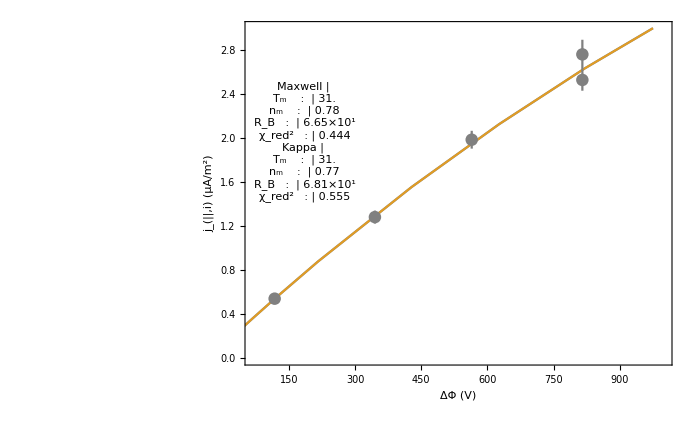

```mathematica
JVPlot=Show[Plot[{kFit[pot],gFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

### J_E-V plot

```mathematica
(*PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kBestJeVKappa,{3,2}]]}),*)
```

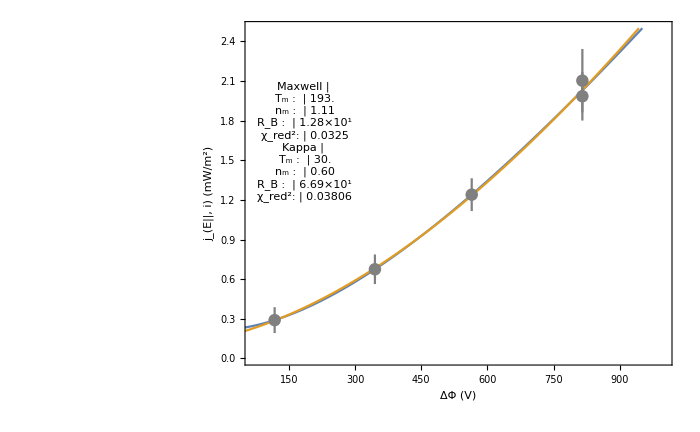

```mathematica
JeVPlot=Show[Plot[{kFitJeV[pot],gFitJeV[pot]},{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",Style[StringForm["J_E-V Fit (`1`)",combTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JeVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jeErrData,PlotStyle->Gray]]
```

### Plots from combined fit

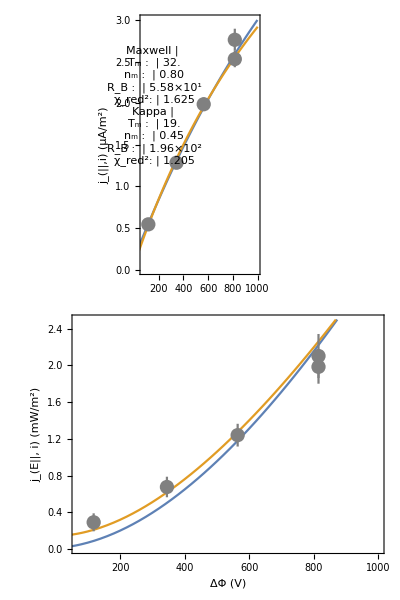

```mathematica
combPlot=Column[{combJVPlot,combJeVPlot}]
```

```mathematica
makePlots=1;
```

```mathematica
(*If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Export[dir<>JeVFilename,JeVPlot];Export[dir<>combJVFilename,combJVPlot];Export[dir<>combJeVFilename,combJeVPlot];Print["Done!"]]*)
```

```mathematica
If[makePlots==1,Print["Making plots in "<>dir<>" ..."];Export[dir<>JVFilename,JVPlot];Print[JeVFilename<>" ..."];Export[dir<>JeVFilename,JeVPlot];Print[combFilename<>" ..."];Export[dir<>combFilename,combPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/20180320/ ...

Orb1612__JeVFit__inds_142-150.png ...

Orb1612__combJVJeVFit__inds_142-150.png ...

Done!

Now everything at once

### Bounds

```mathematica
minFitT=10;
maxFitT=300;
minFitRB=2;
maxFitRB=100000;
minFitN=0.01;
maxFitN=10;
minFitKappa=1.501;
maxFitKappa=35;
```

```mathematica
kConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kCombConstraints={minFitRB<kFitRB<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gCombConstraints={minFitRB<gFitRB<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

```mathematica
kDoubledConstraints={minFitRB<kFitRB1<maxFitRB,minFitRB<kFitRB2<maxFitRB,minFitT<kFitT<maxFitT,minFitN<kFitN<maxFitN,minFitKappa<kFitKappa<maxFitKappa};
gDoubledConstraints={minFitRB<gFitRB1<maxFitRB,minFitRB<gFitRB2<maxFitRB,minFitT<gFitT<maxFitT,minFitN<gFitN<maxFitN};
```

### Initial guesses

```mathematica
kFitNinit=1;
kFitTinit=300;
kFitRBinit=10;
kFitKappainit=10;
kFitRB1init=10;
kFitRB2init=10;
```

```mathematica
gFitNinit=1;
gFitTinit=300;
gFitRBinit=10;
gFitRB1init=10;
gFitRB2init=10;
```

### Setup indices

```mathematica
indsSeg1=inds1;
```

```mathematica
indsSeg2=inds2;
```

```mathematica
(*indsSeg2=Range[162,198]; (*Alt*)*)
```

### Initialize plotData1, errorData1, plotDataWts1, etc.

Current data

```mathematica
{jDataSeg1,jDataSeg2}=(Partition[Riffle[pots[[#]],curs[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jErrDataSeg1,jErrDataSeg2}=(makeErrorData[pots[[#]],curs[[#]],curErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jWtsSeg1,jWtsSeg2}=(1/(curErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

Energy flux data

```mathematica
{jeDataSeg1,jeDataSeg2}=(Partition[Riffle[pots[[#]],jes[[#]]],2])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeErrDataSeg1,jeErrDataSeg2}=(makeErrorData[pots[[#]],jes[[#]],jeErrs[[#]]])&/@{indsSeg1,indsSeg2};
```

```mathematica
{jeWtsSeg1,jeWtsSeg2}=(1/(jeErrs[[#]])^2)&/@{indsSeg1,indsSeg2};
```

```mathematica
RBinit=kBestRB;Tminit=kBestT;nminit=kBestN;kappainit=kBestKappa;
```

```mathematica
combDatSeg1 = Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y}];
```

```mathematica
combDatSeg2 = Join[jDataSeg2/.{x_,y_}->{1,x,y},jeDataSeg2/.{x_,y_}->{2,x,y}];
```

```mathematica
combWtsSeg1=jWtsSeg1~Join~jeWtsSeg1;
```

```mathematica
combWtsSeg2=jWtsSeg2~Join~jeWtsSeg2;
```

```mathematica
doubledDat= Join[jDataSeg1/.{x_,y_}->{1,x,y},jeDataSeg1/.{x_,y_}->{2,x,y},jDataSeg2/.{x_,y_}->{3,x,y},jeDataSeg2/.{x_,y_}->{4,x,y}];
```

```mathematica
doubledWts=jWtsSeg1~Join~jeWtsSeg1~Join~jWtsSeg2~Join~jeWtsSeg2;
```

### Now the doubled double model

```mathematica
kDoubledFitModel[set_,pot_,kFitRB1_,kFitRB2_,kFitT_,kFitN_,kFitKappa_]:=Which[set==1,Evaluate@JVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==2,Evaluate@JEVKappa[pot,kFitRB1,kFitT,kFitN,kFitKappa],set==3,Evaluate@JVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa],set==4,Evaluate@JEVKappa[pot,kFitRB2,kFitT,kFitN,kFitKappa]]
```

```mathematica
gDoubledFitModel[set_,pot_,gFitRB1_,gFitRB2_,gFitT_,gFitN_]:=Which[set==1,Evaluate@JVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==2,Evaluate@JEVMaxwellian[pot,gFitRB1,gFitT,gFitN],set==3,Evaluate@JVMaxwellian[pot,gFitRB2,gFitT,gFitN],set==4,Evaluate@JEVMaxwellian[pot,gFitRB2,gFitT,gFitN]]
```

```mathematica
kDoubledFit=NonlinearModelFit[doubledDat,{kDoubledFitModel[set,pot,kFitRB1,kFitRB2,kFitT,kFitN,kFitKappa],kDoubledConstraints},{{kFitN,kFitNinit},{kFitT,kFitTinit},{kFitRB1,kFitRB1init},{kFitRB2,kFitRB2init},{kFitKappa,kFitKappainit}},{set,pot},Weights->doubledWts]
```

FittedModel[Which[set==1,(0.0266987 «4» Gamma[1+«18»])/((1-1/(«18»)) «1» Gamma[-1/2+«18»]),«4»,«1»,(0.0000268059 «6» Gamma[1+2.04184])/((-2+2.04184) (-1+2.04184) Gamma[-1/2+2.04184])]]

```mathematica
gDoubledFit=NonlinearModelFit[doubledDat,{gDoubledFitModel[set,pot,gFitRB1,gFitRB2,gFitT,gFitN],gDoubledConstraints},{{gFitN,gFitNinit},{gFitT,gFitTinit},{gFitRB1,gFitRB1init},{gFitRB2,gFitRB2init}},{set,pot},Weights->doubledWts]
```

FittedModel[Which[set==1,«6»,0.0000268059 0.508626 121.995 («19»)^(3/2) (2+pot/10.-ⅇ^(-pot/((-1+121.995) «19»)) (2 (1-1/121.995)+pot/10.))]]

```mathematica
kDOF=Length[doubledDat[[;;,1]]]-4;
```

```mathematica
gDOF=Length[doubledDat[[;;,1]]]-3;
```

```mathematica
{kDoubledN,kDoubledT,kDoubledRB1,kDoubledRB2,kDoubledKappa,kDoubledChi2red}=Values@kDoubledFit["BestFitParameters"]~Join~{Total[(kDoubledFit["FitResiduals"])^2*doubledWts]/kDOF};
```

```mathematica
{gDoubledN,gDoubledT,gDoubledRB1,gDoubledRB2,gDoubledChi2red}=Values@gDoubledFit["BestFitParameters"]~Join~{Total[(gDoubledFit["FitResiduals"])^2*doubledWts]/gDOF};
```

### Graphic options

```mathematica
doubledTitlePref="J-V, J_E-V Simult. Fit (`1`)";
```

```mathematica
(*getPadding[g_]:=Module[{im},im=Image[Show[g,LabelStyle->White,Background->White]];
BorderDimensions[im]]*)
```

```mathematica
imgSize=600;
```

```mathematica
{yTitlePad,xTitlePad,topTitlePad}={70,50,50};
{rPad,bPad,blankPad}={25,10,10};
```

```mathematica
TLPad={{yTitlePad,rPad},{bPad,topTitlePad}};
TRPad={{yTitlePad,rPad},{bPad,topTitlePad}};
BLPad={{yTitlePad,rPad},{xTitlePad,blankPad}};
BRPad={{yTitlePad,rPad},{xTitlePad,blankPad}};
```

```mathematica
imgPadding={{60,10},{50,50}};
```

### Now setup plots

```mathematica
(*Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]*)
```

```mathematica
(*JVPlotSeg1=Show[Plot[{JVMaxwellian[pot,gDoubledRB1,gDoubledT,gDoubledN],JVKappa[pot,kDoubledRB1,kDoubledT,kDoubledN,kDoubledKappa]},{pot,minPot,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},PlotLegends->((Style[#,20])&/@{"Maxwellian",StringForm["κ = `1`",NumberForm[kDoubledKappa,{3,2}]]}),Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",combTitle],Bold,25]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize]],ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]]*)
```

```mathematica
doubledRepl={gRB1->gDoubledRB1,gRB2->gDoubledRB2,gTm->gDoubledT,gnm->gDoubledN,gChi2->gDoubledChi2red,kRB1->kDoubledRB1,kRB2->kDoubledRB2,kTm->kDoubledT,knm->kDoubledN,kappa->kDoubledKappa,kChi2->kDoubledChi2red};
```

```mathematica
gDoubledVals1=(MapThread[NumberForm,{({gTm,gnm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB1,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals1=(MapThread[NumberForm,{({kTm,knm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB1,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

```mathematica
gDoubledVals2=(MapThread[NumberForm,{({gTm,gnm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[gRB2,3]/.doubledRepl}~Join~{NumberForm[gChi2,4]/.doubledRepl};
kDoubledVals2=(MapThread[NumberForm,{({kTm,knm}/.doubledRepl),{{3,0},{3,2}}}])~Join~{NumberForm[kRB2,3]/.doubledRepl}~Join~{NumberForm[kChi2,4]/.doubledRepl};
```

#### Parameter tables

```mathematica
doubledParTable1=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{"",Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gDoubledVals1~Join~{"",(ToString@StringForm["`1`",NumberForm[kCombKappa,3]])}~Join~kDoubledVals1}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledParTable2=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{"",Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gDoubledVals2~Join~{"",(ToString@StringForm["`1`",NumberForm[kCombKappa,3]])}~Join~kDoubledVals2}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
doubledTitle1=StringJoin@Riffle[time[[indsSeg1[[{1,-1}]]]],"–"];
```

```mathematica
doubledTitle2=StringJoin@Riffle[time[[indsSeg2[[{1,-1}]]]],"–"];
```

#### Plots (to be shown momentarily)

```mathematica
doubledFitJVPlot1=Plot[Evaluate@(({JVMaxwellian[pot,gRB1,gTm,gnm],JVKappa[pot,kRB1,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",None},{None,Style[StringForm[doubledTitlePref,doubledTitle1],Bold,titleSize]}},ImageSize->imgSize,ImagePadding->TLPad,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable1,Scaled[pTableScaledLoc]]];
```

```mathematica
doubledFitJeVPlot1=Plot[Evaluate@(({JEVMaxwellian[pot,gRB1,gTm,gnm],JEVKappa[pot,kRB1,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{"j_(E||, i) (mW/m^2)",""},{"ΔΦ (V)",""}},FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->imgSize,ImagePadding->BLPad,FrameStyle->Directive[Black,axesLabelSize]];
```

```mathematica
(*Was going to be the version without the legend that works with getPadding function; for some reason the Show function in getPadding hates legends … *)
(*doubledFitJVPlot2NOLEG=Plot[Evaluate@(({JVMaxwellian[pot,gRB2,gTm,gnm],JVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"",""},{"",Style[StringForm[doubledTitlePref,doubledTitle2],Bold,titleSize]}},ImageSize->imgSize,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable2,Scaled[pTableScaledLoc]]];*)
```

```mathematica
doubledFitJVPlot2=Plot[Evaluate@(({JVMaxwellian[pot,gRB2,gTm,gnm],JVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{None,None},{None,Style[StringForm[doubledTitlePref,doubledTitle2],Bold,titleSize]}},ImageSize->imgSize,ImagePadding->TRPad,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},Epilog->Inset[doubledParTable2,Scaled[pTableScaledLoc]]];
```

```mathematica
(*PlotLegends->Map[(Style[#,axesLabelSize])&,{"Maxwellian",StringForm["κ = `1`",NumberForm[(kappa/.doubledRepl),{3,3}]]}],*)
```

```mathematica
doubledFitJeVPlot2=Plot[Evaluate@(({JEVMaxwellian[pot,gRB2,gTm,gnm],JEVKappa[pot,kRB2,kTm,knm,kappa]})/.doubledRepl),{pot,20,maxPot},PlotRange->{{minPot,maxPot},{minJe,maxJe}},Frame->True,FrameLabel->{{None,None},{"ΔΦ (V)",None}},ImageSize->imgSize,ImagePadding->BRPad,FrameStyle->Directive[Black,axesLabelSize],FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}}];
```

```mathematica
(*{p1h,p1v}=getPadding[doubledFitJVPlot1];
{p2h,p2v}=getPadding[doubledFitJVPlot2];*)
```

```mathematica
(*verticalPadding=Max/@Transpose[{p1v,p2v}];*)
```

```mathematica
(*doubledJVPlot1=Show[{doubledFitJVPlot1,ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]},ImagePadding-> {p1h,verticalPadding}];*)
```

```mathematica
(*doubledJVPlot2=Show[{doubledFitJVPlot2,ErrorListPlot[jErrDataSeg2,PlotStyle->Gray]},ImagePadding->{p2h,verticalPadding}];*)
```

```mathematica
doubledJVPlot1=Show[doubledFitJVPlot1,ErrorListPlot[jErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot1=Show[doubledFitJeVPlot1,ErrorListPlot[jeErrDataSeg1,PlotStyle->Gray]];
```

```mathematica
doubledJVPlot2=Show[doubledFitJVPlot2,ErrorListPlot[jErrDataSeg2,PlotStyle->Gray]];
```

```mathematica
doubledJeVPlot2=Show[doubledFitJeVPlot2,ErrorListPlot[jeErrDataSeg2,PlotStyle->Gray]];
```

### Now show plots

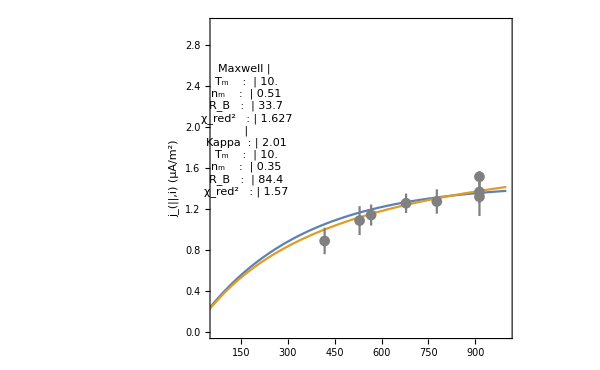
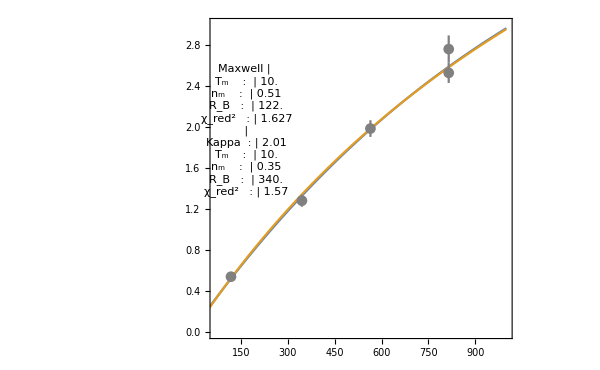
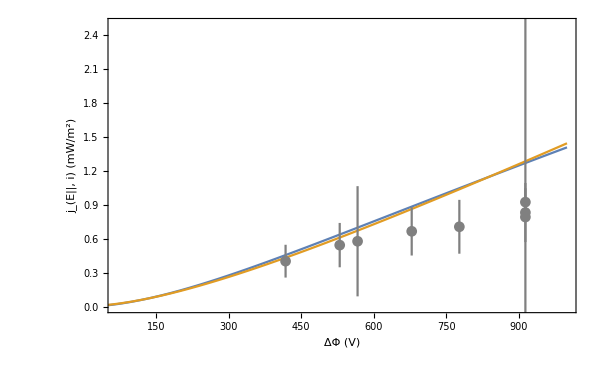
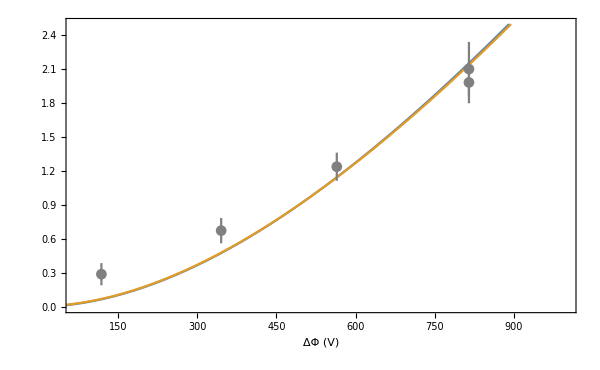
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
doubledPlot=Grid[{{doubledJVPlot1,Framed[doubledJVPlot2,FrameStyle->None,FrameMargins->{{-yTitlePad,0},{0,0}}]},{doubledJeVPlot1,Framed[doubledJeVPlot2,FrameStyle->None,FrameMargins->{{-yTitlePad,0},{0,0}}]}}]
```

Param tables

### J-V params

```mathematica
kFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.772578 | 6.02481 | 0.128233 | 0.918808
kFitT | 31.0539 | 763.246 | 0.0406866 | 0.974112
kFitRB | 68.1331 | 3103.42 | 0.0219542 | 0.986026
kFitKappa | 34.968 | 64235.1 | 0.000544376 | 0.999653

```mathematica
gFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 0.775688 | 0.195529 | 3.96713 | 0.0580614
gFitT | 30.6458 | 24.6243 | 1.24454 | 0.339364
gFitRB | 66.4896 | 23.9099 | 2.78084 | 0.108644

### J_E-V params

```mathematica
kFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitN | 0.598261 | 6.58641 | 0.0908326 | 0.942332
kFitT | 30.2064 | 848.659 | 0.0355931 | 0.97735
kFitRB | 66.8915 | 1627.47 | 0.0411016 | 0.973849
kFitKappa | 2.00998 | 0.550172 | 3.65336 | 0.17009

```mathematica
gFitJeV["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitN | 1.11344 | 0.132185 | 8.42334 | 0.0138028
gFitT | 193.24 | 38.0501 | 5.07857 | 0.0366535
gFitRB | 12.8063 | 12.4226 | 1.03089 | 0.410943

### Params from combined fit

```mathematica
kCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
kFitRB | 196.269 | 355.376 | 0.552288 | 0.600703
kFitT | 18.7191 | 41.9346 | 0.446389 | 0.670975
kFitN | 0.452254 | 0.436179 | 1.03685 | 0.339773
kFitKappa | 2.00561 | 0.0257765 | 77.8079 | 3.03411×10^-10

```mathematica
gCombFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
gFitRB | 55.822 | 22.2385 | 2.51015 | 0.0403881
gFitT | 31.9975 | 24.8822 | 1.28596 | 0.239358
gFitN | 0.801642 | 0.192171 | 4.1715 | 0.00418131